## Construct and Parameterize One Enzyme Module

```mathematica
Quit[]
```

## Initializing the Notebook

```mathematica
<<Toolbox`;
<<MASSef`;

SetDirectory[NotebookDirectory[]];

removeInputFiles = True;
removeOutputFiles = True;

rxnName="PYK2";
fitLabel=rxnName;
dataFileName=rxnName;

assumedUncertaintyFraction = 0.05;
(*Q10 Correction Options*)
Q10KcatCorrectionFlag = True; (*True if kcats should be corrected to physiological T*)
TPhysiological = 37; (*C*)
Q10=2.5;


(* user will need to change this path *)
(*pathMASSef = "/home/mrama/Dropbox/MASSef/";*)
pathMASSef = "C:/MASSef/";
kineticDataFileName =  "kinetic_data_MASSpy.csv";

mainFolder = "fit_PYK2_MASSpy_typeII";
{pathData, inputPath, outputPath}=initializeNotebook[pathMASSef, mainFolder, removeInputFiles, removeOutputFiles];
```

Molecule::shdw: Symbol Molecule appears in multiple contexts {AutomaticUnits`,System`}; definitions in context AutomaticUnits` may shadow or be shadowed by other definitions.

Working dir:C:\MASSef\examples\

## Import Data

```mathematica
{rxn, mechanism, structure, nActiveSites, nAllostericSites, KeqList0,kmList0, s05List0, kcatList0, inhibitionList0, activationList0, otherParmsList0, bufferInfo, ionCharge}= importAllData [rxnName, pathData, kineticDataFileName, assumedUncertaintyFraction, Q10KcatCorrectionFlag, TPhysiological, Q10];
```

(adp^c+pep^c→atp^c+pyr^c)^PYK2

;

Structure:

Active sites:

Keq Values:

Priority | Substrate | Keq_Value | Uncertainty | CoSubstrate | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations
1 | adp | Null
pep | Null | 22000 | 20900.
23100. | Null | Null | 7.5 | Null | Null | Null

Km Values:

Priority | Substrate | Km_Value | Uncertainty | CoSubstrate | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations
1 | adp | 0.00017 | 0.0001615
0.0001785 | pep | 0.005 | M | 7.5 | 25 | hepes | 0.01 | mg2 | 0.01
cl | 0.02
cl | 0.05
k | 0.05
1 | adp | 0.00012 | 0.000114
0.000126 | pep | 0.0005
r5p | 0.001 | M | 7.5 | 25 | hepes | 0.01 | mg2 | 0.01
cl | 0.02
cl | 0.05
k | 0.05
1 | adp | 0.00012 | 0.000114
0.000126 | pep | 0.005
r5p | 0.001 | M | 7.5 | 25 | hepes | 0.01 | mg2 | 0.01
cl | 0.02
cl | 0.05
k | 0.05

S0.5 Values:

Priority | Substrate | S0.5_Value | Uncertainty | CoSubstrate | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations
1 | pep | 0.00082 | 0.000779
0.000861 |  | M | 7.5 | 25 | hepes | 0.01 | mg2 | 0.01
cl | 0.02
cl | 0.05
k | 0.05
1 | pep | 0.00019 | 0.0001805
0.0001995 | amp | 0.002 | M | 7.5 | 25 | hepes | 0.01 | mg2 | 0.01
cl | 0.02
cl | 0.05
k | 0.05
1 | pep | 0.00013 | 0.0001235
0.0001365 | g6p | 0.001 | M | 7.5 | 25 | hepes | 0.01 | mg2 | 0.01
cl | 0.02
cl | 0.05
k | 0.05
1 | pep | 0.0007 | 0.000665
0.000735 | r5p | 0.001 | M | 7.5 | 25 | hepes | 0.01 | mg2 | 0.01
cl | 0.02
cl | 0.05
k | 0.05
1 | pep | 0.00082 | 0.000779
0.000861 | pi | 0.001 | M | 7.5 | 25 | hepes | 0.01 | mg2 | 0.01
cl | 0.02
cl | 0.05
k | 0.05
1 | adp | 0.00036 | 0.000342
0.000378 | pep | 0.0005 | M | 7.5 | 25 | hepes | 0.01 | mg2 | 0.01
cl | 0.02
cl | 0.05
k | 0.05

kcat Values:

Priority | Metabolite(s) | Value | Uncertainty | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations
1 | pep | Null
adp | Null | 30.0281 | 28.5267
31.5295 | 1/s | 7 | 37 |  |

Inhibition Values:

Priority | Parameter_Type | Inhibitor | Value | Uncertainty | Cosubstrates | Inhibition Type | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations

Activation Values:

Priority | Parameter_Type | Activator | Value | Uncertainty | Cosubstrates | Activation Type | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations

Other Parameters:

Priority | Parameter_Type | Metabolite | Value | Uncertainty | Cosubstrates | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations
1 | n | pep | 1.58 | 1.501
1.659 |  |  | 7.5 | 25 | hepes | 0.01 | mg2 | 0.01
cl | 0.02
cl | 0.05
k | 0.05
1 | n | pep | 1.03 | 0.9785
1.0815 | amp | 0.002 |  | 7.5 | 25 | hepes | 0.01 | mg2 | 0.01
cl | 0.02
cl | 0.05
k | 0.05
1 | n | pep | 1 | 0.95
1.05 | g6p | 0.001 |  | 7.5 | 25 | hepes | 0.01 | mg2 | 0.01
cl | 0.02
cl | 0.05
k | 0.05
1 | n | pep | 0.99 | 0.9405
1.0395 | r5p | 0.001 |  | 7.5 | 25 | hepes | 0.01 | mg2 | 0.01
cl | 0.02
cl | 0.05
k | 0.05
1 | n | pep | 2.1 | 1.995
2.205 | pi | 0.001 |  | 7.5 | 25 | hepes | 0.01 | mg2 | 0.01
cl | 0.02
cl | 0.05
k | 0.05
1 | n | adp | 2 | 1.5
3 | pep | 0.0005 |  | 7.5 | 25 | hepes | 0.01 | mg2 | 0.01
cl | 0.02
cl | 0.05
k | 0.05

### Define data points priority

```mathematica
(* data point priorities should be between 0 and 1 
  if a given data point has priority 0, it will be discarded
  by default all data points priority is set to 1 *)

KeqPriorities = {1};
kmPriorities = {1,1,1};
s05Priorities = {0,0,0,0,0,0};
kcatPriorities = {1};
inhibitionPriorities=Null;
activationPriorities = Null;
otherParamsPriorities = {0,0,0,0,0,0};

{KeqList, kmList, s05List, kcatList, inhibitionList, activationList, otherParmsList}= updateDataPriorities[KeqPriorities, kmPriorities, s05Priorities, kcatPriorities, inhibitionPriorities, activationPriorities, otherParamsPriorities,
					 KeqList0,kmList0, s05List0, kcatList0, inhibitionList0, activationList0, otherParmsList0];

printEnzymeData[rxn, mechanism, structure, nActiveSites,  KeqList, kmList, s05List, kcatList, inhibitionList, activationList, otherParmsList];
```

(adp^c+pep^c→atp^c+pyr^c)^PYK2

;

Structure:

Active sites:

Keq Values:

Priority | Substrate | Keq_Value | Uncertainty | CoSubstrate | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations
1 | adp | Null
pep | Null | 22000 | 20900.
23100. | Null | Null | 7.5 | Null | Null | Null

Km Values:

Priority | Substrate | Km_Value | Uncertainty | CoSubstrate | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations
1 | adp | 0.00017 | 0.0001615
0.0001785 | pep | 0.005 | M | 7.5 | 25 | hepes | 0.01 | mg2 | 0.01
cl | 0.02
cl | 0.05
k | 0.05
1 | adp | 0.00012 | 0.000114
0.000126 | pep | 0.0005
r5p | 0.001 | M | 7.5 | 25 | hepes | 0.01 | mg2 | 0.01
cl | 0.02
cl | 0.05
k | 0.05
1 | adp | 0.00012 | 0.000114
0.000126 | pep | 0.005
r5p | 0.001 | M | 7.5 | 25 | hepes | 0.01 | mg2 | 0.01
cl | 0.02
cl | 0.05
k | 0.05

S0.5 Values:

Priority | Substrate | S0.5_Value | Uncertainty | CoSubstrate | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations

kcat Values:

Priority | Metabolite(s) | Value | Uncertainty | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations
1 | pep | Null
adp | Null | 30.0281 | 28.5267
31.5295 | 1/s | 7 | 37 |  |

Inhibition Values:

Priority | Parameter_Type | Inhibitor | Value | Uncertainty | Cosubstrates | Inhibition Type | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations

Activation Values:

Priority | Parameter_Type | Activator | Value | Uncertainty | Cosubstrates | Activation Type | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations

Other Parameters:

Priority | Parameter_Type | Metabolite | Value | Uncertainty | Cosubstrates | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations

## Define enzyme mechanism and catalytic tracks

### Define enzyme mechanism

```mathematica
Overscript[adp^c+pep^c->atp^c+pyr^c, PYK2]
```

```mathematica
catalyticBranch={"E_PYK2[c] + adp[c] <=> E_PYK2[c]&adp",
				"E_PYK2[c]&adp + pep[c] <=> E_PYK2[c]&pep&adp",
				"E_PYK2[c]&pep&adp <=> E_PYK2[c]&pyr&atp",
				"E_PYK2[c]&pyr&atp <=> E_PYK2[c]&atp + pyr[c]",
				"E_PYK2[c]&atp <=> E_PYK2[c] + atp[c]"};


enzymeModel=constructEnzymeModule[Mechanism->catalyticBranch,Activators->{},ActivationSites->0,Inhibitors->{},InhibitionSites->0];
enzymeModel["Reactions"]
```

{((PYK2^c)_^+adp^c⇌(PYK2^c&adp^c)_^)^PYK21,((PYK2^c&atp^c)_^⇌(PYK2^c)_^+atp^c)^PYK22,((PYK2^c&adp^c)_^+pep^c⇌(PYK2^c&pep^c&adp^c)_^)^PYK23,((PYK2^c&pyr^c&atp^c)_^⇌(PYK2^c&atp^c)_^+pyr^c)^PYK24,((PYK2^c&pep^c&adp^c)_^⇌(PYK2^c&pyr^c&atp^c)_^)^PYK25}

### Define all catalytic tracks

```mathematica
catalyticReactionsSet1={((PYK2^c)_^+adp^c⇌(PYK2^c&adp^c)_^)^PYK21,Overscript[(PYK2^c&atp^c)_^⇌(PYK2^c)_^+atp^c, PYK22],((PYK2^c&adp^c)_^+pep^c⇌(PYK2^c&pep^c&adp^c)_^)^PYK23,Overscript[(PYK2^c&pyr^c&atp^c)_^⇌(PYK2^c&atp^c)_^+pyr^c, PYK24],((PYK2^c&pep^c&adp^c)_^⇌(PYK2^c&pyr^c&atp^c)_^)^PYK25};
catalyticReactionsSetsList = {catalyticReactionsSet1};
```

## Set up rate equations

```mathematica
MWCFlag=False;
nActiveSites=1;
assumedSaturatingConc = 1;
simplifyFlag=True;
simplifyMaxTime=30;
otherMetsReverseZeroSub={};
 otherMetsForwardZeroSub ={};

{enzymeModel, haldaneRatiosList,  metSatForSub, metSatRevSub,  finalRateConsts, metsFull, metsSub, rateConstsSub, 
			fileList, fileListSub, eqnNameList,eqnValList, eqnValListPy, 
			allCatalyticReactions,nonCatalyticReactions, unifiedRateConstList, 
			absoluteFlux, absoluteRateForward, absoluteRateReverse, relativeRateForward, relativeRateReverse, 
			otherAbsoluteRatesForward, otherAbsoluteRatesReverse}=

	setUpRateEquations[enzymeModel, rxn, rxnName, inputPath, inhibitionList, inhibitionList, catalyticReactionsSetsList, otherMetsReverseZeroSub,  
						 otherMetsForwardZeroSub,  MWCFlag, simplifyFlag, simplifyMaxTime, nActiveSites, assumedSaturatingConc];
```

Added inhibition reactions:

{}

Generating flux equation...

{((PYK2^c&pep^c&adp^c)_^-((PYK2^c&pyr^c&atp^c)_^)/K_PYK25) Volume_c k_PYK25^⟶}

Volume_c (-(PYK2^c&pyr^c&atp^c)_^ k_PYK25^⟵+(PYK2^c&pep^c&adp^c)_^ k_PYK25^⟶)

Simplifying...

Generating absolute rate forward equation...

Simplifying...

Generating absolute rate reverse equation...

Simplifying...

Generating relative rate forward equation...

Simplifying...

Generating relative rate forward equation...

Simplifying...

Generating relative rate reverse equation...

Simplifying...

Generating relative rate reverse equation...

Simplifying...

Generating Haldane Relations...

Defining rate constant and metabolite substitutions for export...

Exporting equations...

## Simulate Data

```mathematica
(* format: {priority, ratio or other custom equation, value, value range (uncertainty) *)
customRatiosDataList={};
```

### Simulate data without uncertainty

```mathematica
{allFittingData, dataPathList, fileList, fileListSub}= simulateData[enzymeModel,dataFileName,fitLabel, haldaneRatiosList, KeqList, kmList, s05List, kcatList, inhibitionList, activationList, otherParmsList, rxn, metsFull,  
			metSatForSub, metSatRevSub,  bufferInfo, ionCharge, inputPath,  fileList, fileListSub, 
			eqnNameList,eqnValList, eqnValListPy, eqnNameList, rateConstsSub, 
			metsSub, allCatalyticReactions,nonCatalyticReactions, unifiedRateConstList, customRatiosDataList, assumedSaturatingConc];
```

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

```mathematica
FilePrint@dataPathList
```

Priority	13dpg[c]	g3p[c]	nad[c]	nadh[c]	pi[c]	param_GAPD_total	param_pH	param_Temp	FileFlag	Target_Data
1	0	0	0	0	0	1	7.5	25	"C:\MASSef\examples\fit_GAPD_MASSpy_typeII\input\haldaneRatio_1.txt"	0.452
1	0	0	0	0	0	1	7.5	25	"C:\MASSef\examples\fit_GAPD_MASSpy_typeII\input\haldaneRatio_1.txt"	0.452
1	0	0	0	0	0	1	7.5	25	"C:\MASSef\examples\fit_GAPD_MASSpy_typeII\input\haldaneRatio_1.txt"	0.452
1	0	0	0	0	0	1	7.5	25	"C:\MASSef\examples\fit_GAPD_MASSpy_typeII\input\haldaneRatio_1.txt"	0.452
1	0	0	0	0	0	1	7.5	25	"C:\MASSef\examples\fit_GAPD_MASSpy_typeII\input\haldaneRatio_1.txt"	0.452
1	0	0	0	0	0	1	7.5	25	"C:\MASSef\examples\fit_GAPD_MASSpy_typeII\input\haldaneRatio_1.txt"	0.452
1	0	0	0	0	0	1	7.5	25	"C:\MASSef\examples\fit_GAPD_MASSpy_typeII\input\haldaneRatio_1.txt"	0.452
1	0	0	0	0	0	1	7.5	25	"C:\MASSef\examples\fit_GAPD_MASSpy_typeII\input\haldaneRatio_1.txt"	0.452
1	0	0	0	0	0	1	7.5	25	"C:\MASSef\examples\fit_GAPD_MASSpy_typeII\input\haldaneRatio_1.txt"	0.452
1	0	0	0	0	0	1	7.5	25	"C:\MASSef\examples\fit_GAPD_MASSpy_typeII\input\haldaneRatio_1.txt"	0.452
1	0	0	0	0	0	1	7.5	25	"C:\MASSef\examples\fit_GAPD_MASSpy_typeII\input\haldaneRatio_1.txt"	0.452
1	0	0.089	4.500000000000003e-6	0	0.053	1	8.9	22	"C:\MASSef\examples\fit_GAPD_MASSpy_typeII\input\relRateFor_nad.txt"	0.09090909090909095
1	0	0.089	7.132019366075018e-6	0	0.053	1	8.9	22	"C:\MASSef\examples\fit_GAPD_MASSpy_typeII\input\relRateFor_nad.txt"	0.13680688860321014
1	0	0.089	0.000011303488941793127	0	0.053	1	8.9	22	"C:\MASSef\examples\fit_GAPD_MASSpy_typeII\input\relRateFor_nad.txt"	0.20076000891310194
1	0	0.089	0.000017914822674907372	0	0.053	1	8.9	22	"C:\MASSef\examples\fit_GAPD_MASSpy_typeII\input\relRateFor_nad.txt"	0.28474724895080133
1	0	0.089	0.000028393080501608703	0	0.053	1	8.9	22	"C:\MASSef\examples\fit_GAPD_MASSpy_typeII\input\relRateFor_nad.txt"	0.386863179846857
1	0	0.089	0.00004500000000000003	0	0.053	1	8.9	22	"C:\MASSef\examples\fit_GAPD_MASSpy_typeII\input\relRateFor_nad.txt"	0.5000000000000002
1	0	0.089	0.00007132019366075018	0	0.053	1	8.9	22	"C:\MASSef\examples\fit_GAPD_MASSpy_typeII\input\relRateFor_nad.txt"	0.6131368201531432
1	0	0.089	0.00011303488941793127	0	0.053	1	8.9	22	"C:\MASSef\examples\fit_GAPD_MASSpy_typeII\input\relRateFor_nad.txt"	0.7152527510491989
1	0	0.089	0.0001791482267490739	0	0.053	1	8.9	22	"C:\MASSef\examples\fit_GAPD_MASSpy_typeII\input\relRateFor_nad.txt"	0.7992399910868984
1	0	0.089	0.00028393080501608705	0	0.053	1	8.9	22	"C:\MASSef\examples\fit_GAPD_MASSpy_typeII\input\relRateFor_nad.txt"	0.86319311139679
1	0	0.089	0.00045000000000000026	0	0.053	1	8.9	22	"C:\MASSef\examples\fit_GAPD_MASSpy_typeII\input\relRateFor_nad.txt"	0.9090909090909093
1	0	0.00008900000000000009	0.0045	0	0.053	1	8.9	22	"C:\MASSef\examples\fit_GAPD_MASSpy_typeII\input\relRateFor_g3p.txt"	0.090909090909091
1	0	0.00014105549412903932	0.0045	0	0.053	1	8.9	22	"C:\MASSef\examples\fit_GAPD_MASSpy_typeII\input\relRateFor_g3p.txt"	0.1368068886032102
1	0	0.00022355789240435282	0.0045	0	0.053	1	8.9	22	"C:\MASSef\examples\fit_GAPD_MASSpy_typeII\input\relRateFor_g3p.txt"	0.2007600089131019
1	0	0.000354315381792613	0.0045	0	0.053	1	8.9	22	"C:\MASSef\examples\fit_GAPD_MASSpy_typeII\input\relRateFor_g3p.txt"	0.2847472489508017
1	0	0.0005615520365873723	0.0045	0	0.053	1	8.9	22	"C:\MASSef\examples\fit_GAPD_MASSpy_typeII\input\relRateFor_g3p.txt"	0.3868631798468571
1	0	0.0008900000000000009	0.0045	0	0.053	1	8.9	22	"C:\MASSef\examples\fit_GAPD_MASSpy_typeII\input\relRateFor_g3p.txt"	0.5000000000000003
1	0	0.0014105549412903931	0.0045	0	0.053	1	8.9	22	"C:\MASSef\examples\fit_GAPD_MASSpy_typeII\input\relRateFor_g3p.txt"	0.6131368201531434
1	0	0.0022355789240435303	0.0045	0	0.053	1	8.9	22	"C:\MASSef\examples\fit_GAPD_MASSpy_typeII\input\relRateFor_g3p.txt"	0.7152527510491988
1	0	0.00354315381792613	0.0045	0	0.053	1	8.9	22	"C:\MASSef\examples\fit_GAPD_MASSpy_typeII\input\relRateFor_g3p.txt"	0.7992399910868984
1	0	0.005615520365873723	0.0045	0	0.053	1	8.9	22	"C:\MASSef\examples\fit_GAPD_MASSpy_typeII\input\relRateFor_g3p.txt"	0.86319311139679
1	0	0.008900000000000009	0.0045	0	0.053	1	8.9	22	"C:\MASSef\examples\fit_GAPD_MASSpy_typeII\input\relRateFor_g3p.txt"	0.9090909090909092
1	0	0.089	0.0045	0	0.000053000000000000014	1	8.9	22	"C:\MASSef\examples\fit_GAPD_MASSpy_typeII\input\relRateFor_pi.txt"	0.09090909090909094
1	0	0.089	0.0045	0	0.00008399933920043907	1	8.9	22	"C:\MASSef\examples\fit_GAPD_MASSpy_typeII\input\relRateFor_pi.txt"	0.13680688860321008
1	0	0.089	0.0045	0	0.00013312998087000775	1	8.9	22	"C:\MASSef\examples\fit_GAPD_MASSpy_typeII\input\relRateFor_pi.txt"	0.20076000891310175
1	0	0.089	0.0045	0	0.00021099680039335364	1	8.9	22	"C:\MASSef\examples\fit_GAPD_MASSpy_typeII\input\relRateFor_pi.txt"	0.2847472489508015
1	0	0.089	0.0045	0	0.00033440739257450236	1	8.9	22	"C:\MASSef\examples\fit_GAPD_MASSpy_typeII\input\relRateFor_pi.txt"	0.3868631798468569
1	0	0.089	0.0045	0	0.0005300000000000001	1	8.9	22	"C:\MASSef\examples\fit_GAPD_MASSpy_typeII\input\relRateFor_pi.txt"	0.5
1	0	0.089	0.0045	0	0.0008399933920043907	1	8.9	22	"C:\MASSef\examples\fit_GAPD_MASSpy_typeII\input\relRateFor_pi.txt"	0.6131368201531432
1	0	0.089	0.0045	0	0.0013312998087000789	1	8.9	22	"C:\MASSef\examples\fit_GAPD_MASSpy_typeII\input\relRateFor_pi.txt"	0.7152527510491988
1	0	0.089	0.0045	0	0.0021099680039335365	1	8.9	22	"C:\MASSef\examples\fit_GAPD_MASSpy_typeII\input\relRateFor_pi.txt"	0.7992399910868982
1	0	0.089	0.0045	0	0.0033440739257450235	1	8.9	22	"C:\MASSef\examples\fit_GAPD_MASSpy_typeII\input\relRateFor_pi.txt"	0.8631931113967899
1	0	0.089	0.0045	0	0.005300000000000002	1	8.9	22	"C:\MASSef\examples\fit_GAPD_MASSpy_typeII\input\relRateFor_pi.txt"	0.9090909090909092
1	0	1	1	0	1	1	8.9	37	"C:\MASSef\examples\fit_GAPD_MASSpy_typeII\input\absRateFor.txt"	1059.363016156407
1	0	1	1	0	1	1	8.9	37	"C:\MASSef\examples\fit_GAPD_MASSpy_typeII\input\absRateFor.txt"	1059.363016156407
1	0	1	1	0	1	1	8.9	37	"C:\MASSef\examples\fit_GAPD_MASSpy_typeII\input\absRateFor.txt"	1059.363016156407
1	0	1	1	0	1	1	8.9	37	"C:\MASSef\examples\fit_GAPD_MASSpy_typeII\input\absRateFor.txt"	1059.363016156407
1	0	1	1	0	1	1	8.9	37	"C:\MASSef\examples\fit_GAPD_MASSpy_typeII\input\absRateFor.txt"	1059.363016156407
1	0	1	1	0	1	1	8.9	37	"C:\MASSef\examples\fit_GAPD_MASSpy_typeII\input\absRateFor.txt"	1059.363016156407
1	0	1	1	0	1	1	8.9	37	"C:\MASSef\examples\fit_GAPD_MASSpy_typeII\input\absRateFor.txt"	1059.363016156407
1	0	1	1	0	1	1	8.9	37	"C:\MASSef\examples\fit_GAPD_MASSpy_typeII\input\absRateFor.txt"	1059.363016156407
1	0	1	1	0	1	1	8.9	37	"C:\MASSef\examples\fit_GAPD_MASSpy_typeII\input\absRateFor.txt"	1059.363016156407
1	0	1	1	0	1	1	8.9	37	"C:\MASSef\examples\fit_GAPD_MASSpy_typeII\input\absRateFor.txt"	1059.363016156407
1	0	1	1	0	1	1	8.9	37	"C:\MASSef\examples\fit_GAPD_MASSpy_typeII\input\absRateFor.txt"	1059.363016156407
1	1	0	0	1	0	1	7	37	"C:\MASSef\examples\fit_GAPD_MASSpy_typeII\input\absRateRev.txt"	30.028110849535786
1	1	0	0	1	0	1	7	37	"C:\MASSef\examples\fit_GAPD_MASSpy_typeII\input\absRateRev.txt"	30.028110849535786
1	1	0	0	1	0	1	7	37	"C:\MASSef\examples\fit_GAPD_MASSpy_typeII\input\absRateRev.txt"	30.028110849535786
1	1	0	0	1	0	1	7	37	"C:\MASSef\examples\fit_GAPD_MASSpy_typeII\input\absRateRev.txt"	30.028110849535786
1	1	0	0	1	0	1	7	37	"C:\MASSef\examples\fit_GAPD_MASSpy_typeII\input\absRateRev.txt"	30.028110849535786
1	1	0	0	1	0	1	7	37	"C:\MASSef\examples\fit_GAPD_MASSpy_typeII\input\absRateRev.txt"	30.028110849535786
1	1	0	0	1	0	1	7	37	"C:\MASSef\examples\fit_GAPD_MASSpy_typeII\input\absRateRev.txt"	30.028110849535786
1	1	0	0	1	0	1	7	37	"C:\MASSef\examples\fit_GAPD_MASSpy_typeII\input\absRateRev.txt"	30.028110849535786
1	1	0	0	1	0	1	7	37	"C:\MASSef\examples\fit_GAPD_MASSpy_typeII\input\absRateRev.txt"	30.028110849535786
1	1	0	0	1	0	1	7	37	"C:\MASSef\examples\fit_GAPD_MASSpy_typeII\input\absRateRev.txt"	30.028110849535786
1	1	0	0	1	0	1	7	37	"C:\MASSef\examples\fit_GAPD_MASSpy_typeII\input\absRateRev.txt"	30.028110849535786
1	0	0	0	0	0	1	7.5	25	"C:\MASSef\examples\fit_GAPD_MASSpy_typeII\input\KdRatio_nad.txt"	3.2e-7
1	0	0	0	0	0	1	7.5	25	"C:\MASSef\examples\fit_GAPD_MASSpy_typeII\input\KdRatio_nad.txt"	3.2e-7
1	0	0	0	0	0	1	7.5	25	"C:\MASSef\examples\fit_GAPD_MASSpy_typeII\input\KdRatio_nad.txt"	3.2e-7
1	0	0	0	0	0	1	7.5	25	"C:\MASSef\examples\fit_GAPD_MASSpy_typeII\input\KdRatio_nad.txt"	3.2e-7
1	0	0	0	0	0	1	7.5	25	"C:\MASSef\examples\fit_GAPD_MASSpy_typeII\input\KdRatio_nad.txt"	3.2e-7
1	0	0	0	0	0	1	7.5	25	"C:\MASSef\examples\fit_GAPD_MASSpy_typeII\input\KdRatio_nad.txt"	3.2e-7
1	0	0	0	0	0	1	7.5	25	"C:\MASSef\examples\fit_GAPD_MASSpy_typeII\input\KdRatio_nad.txt"	3.2e-7
1	0	0	0	0	0	1	7.5	25	"C:\MASSef\examples\fit_GAPD_MASSpy_typeII\input\KdRatio_nad.txt"	3.2e-7
1	0	0	0	0	0	1	7.5	25	"C:\MASSef\examples\fit_GAPD_MASSpy_typeII\input\KdRatio_nad.txt"	3.2e-7
1	0	0	0	0	0	1	7.5	25	"C:\MASSef\examples\fit_GAPD_MASSpy_typeII\input\KdRatio_nad.txt"	3.2e-7
1	0	0	0	0	0	1	7.5	25	"C:\MASSef\examples\fit_GAPD_MASSpy_typeII\input\KdRatio_nad.txt"	3.2e-7
1	0	0	0	0	0	1	7.5	25	"C:\MASSef\examples\fit_GAPD_MASSpy_typeII\input\customRatio_1.txt"	425.
1	0	0	0	0	0	1	7.5	25	"C:\MASSef\examples\fit_GAPD_MASSpy_typeII\input\customRatio_1.txt"	425.
1	0	0	0	0	0	1	7.5	25	"C:\MASSef\examples\fit_GAPD_MASSpy_typeII\input\customRatio_1.txt"	425.
1	0	0	0	0	0	1	7.5	25	"C:\MASSef\examples\fit_GAPD_MASSpy_typeII\input\customRatio_1.txt"	425.
1	0	0	0	0	0	1	7.5	25	"C:\MASSef\examples\fit_GAPD_MASSpy_typeII\input\customRatio_1.txt"	425.
1	0	0	0	0	0	1	7.5	25	"C:\MASSef\examples\fit_GAPD_MASSpy_typeII\input\customRatio_1.txt"	425.
1	0	0	0	0	0	1	7.5	25	"C:\MASSef\examples\fit_GAPD_MASSpy_typeII\input\customRatio_1.txt"	425.
1	0	0	0	0	0	1	7.5	25	"C:\MASSef\examples\fit_GAPD_MASSpy_typeII\input\customRatio_1.txt"	425.
1	0	0	0	0	0	1	7.5	25	"C:\MASSef\examples\fit_GAPD_MASSpy_typeII\input\customRatio_1.txt"	425.
1	0	0	0	0	0	1	7.5	25	"C:\MASSef\examples\fit_GAPD_MASSpy_typeII\input\customRatio_1.txt"	425.
1	0	0	0	0	0	1	7.5	25	"C:\MASSef\examples\fit_GAPD_MASSpy_typeII\input\customRatio_1.txt"	425.

### Simulate data with uncertainty

```mathematica
nSamples=10;
SeedRandom[1234];
{allFittingDataList, dataPathList, fileList, fileListSub}=simulateDataWithUncertainty[nSamples,enzymeModel,dataFileName,fitLabel, haldaneRatiosList, KeqList, kmList, s05List, kcatList, inhibitionList, activationList, otherParmsList, rxn, metsFull,  metSatForSub, metSatRevSub, otherParmsList,  bufferInfo, ionCharge, inputPath,  fileList, 
							fileListSub, eqnNameList,eqnValList, eqnValListPy, eqnNameList, rateConstsSub, 
							metsSub, allCatalyticReactions,nonCatalyticReactions, unifiedRateConstList,  customRatiosDataList, assumedSaturatingConc];
```

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating other data...

Simulating custom ratios data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating other data...

Simulating custom ratios data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating other data...

Simulating custom ratios data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating other data...

Simulating custom ratios data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating other data...

Simulating custom ratios data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating other data...

Simulating custom ratios data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating other data...

Simulating custom ratios data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating other data...

Simulating custom ratios data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating other data...

Simulating custom ratios data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating other data...

Simulating custom ratios data...

```mathematica
FilePrint[dataPathList[[1]]]
```

Priority	13dpg[c]	g3p[c]	nad[c]	nadh[c]	pi[c]	param_GAPD_total	param_pH	param_Temp	FileFlag	Target_Data
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/haldaneRatio_1.txt"	0.4405116176334556
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/haldaneRatio_1.txt"	0.4405116176334556
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/haldaneRatio_1.txt"	0.4405116176334556
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/haldaneRatio_1.txt"	0.4405116176334556
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/haldaneRatio_1.txt"	0.4405116176334556
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/haldaneRatio_1.txt"	0.4405116176334556
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/haldaneRatio_1.txt"	0.4405116176334556
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/haldaneRatio_1.txt"	0.4405116176334556
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/haldaneRatio_1.txt"	0.4405116176334556
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/haldaneRatio_1.txt"	0.4405116176334556
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/haldaneRatio_1.txt"	0.4405116176334556
1	0	0.089	3.8624414067610525e-6	0	0.053	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_nad.txt"	0.09090909090909095
1	0	0.089	6.1215570918555205e-6	0	0.053	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_nad.txt"	0.1368068886032101
1	0	0.089	9.702014162143871e-6	0	0.053	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_nad.txt"	0.20076000891310197
1	0	0.089	0.00001537665619874311	0	0.053	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_nad.txt"	0.2847472489508014
1	0	0.089	0.000024370357732202946	0	0.053	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_nad.txt"	0.38686317984685703
1	0	0.089	0.00003862441406761052	0	0.053	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_nad.txt"	0.5000000000000001
1	0	0.089	0.0000612155709185552	0	0.053	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_nad.txt"	0.6131368201531432
1	0	0.089	0.0000970201416214387	0	0.053	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_nad.txt"	0.7152527510491988
1	0	0.089	0.00015376656198743123	0	0.053	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_nad.txt"	0.7992399910868984
1	0	0.089	0.00024370357732202944	0	0.053	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_nad.txt"	0.86319311139679
1	0	0.089	0.00038624414067610526	0	0.053	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_nad.txt"	0.9090909090909091
1	0	0.0001345263278918314	0.0045	0	0.053	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_g3p.txt"	0.09090909090909088
1	0	0.0002132098612825553	0.0045	0	0.053	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_g3p.txt"	0.13680688860321
1	0	0.00033791485771230003	0.0045	0	0.053	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_g3p.txt"	0.20076000891310167
1	0	0.0005355589576196904	0.0045	0	0.053	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_g3p.txt"	0.2847472489508014
1	0	0.0008488037460930167	0.0045	0	0.053	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_g3p.txt"	0.3868631798468568
1	0	0.0013452632789183142	0.0045	0	0.053	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_g3p.txt"	0.49999999999999994
1	0	0.002132098612825553	0.0045	0	0.053	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_g3p.txt"	0.613136820153143
1	0	0.0033791485771230037	0.0045	0	0.053	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_g3p.txt"	0.7152527510491987
1	0	0.005355589576196904	0.0045	0	0.053	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_g3p.txt"	0.7992399910868981
1	0	0.008488037460930166	0.0045	0	0.053	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_g3p.txt"	0.8631931113967899
1	0	0.013452632789183142	0.0045	0	0.053	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_g3p.txt"	0.909090909090909
1	0	0.089	0.0045	0	0.00004095978570257995	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_pi.txt"	0.0909090909090909
1	0	0.089	0.0045	0	0.00006491688552468503	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_pi.txt"	0.13680688860321005
1	0	0.089	0.0045	0	0.00010288632994385063	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_pi.txt"	0.20076000891310167
1	0	0.089	0.0045	0	0.00016306384392531697	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_pi.txt"	0.2847472489508014
1	0	0.089	0.0045	0	0.0002584387761737762	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_pi.txt"	0.3868631798468568
1	0	0.089	0.0045	0	0.00040959785702579944	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_pi.txt"	0.5
1	0	0.089	0.0045	0	0.0006491688552468503	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_pi.txt"	0.6131368201531432
1	0	0.089	0.0045	0	0.0010288632994385075	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_pi.txt"	0.7152527510491987
1	0	0.089	0.0045	0	0.0016306384392531697	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_pi.txt"	0.7992399910868982
1	0	0.089	0.0045	0	0.002584387761737762	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_pi.txt"	0.86319311139679
1	0	0.089	0.0045	0	0.004095978570257995	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_pi.txt"	0.9090909090909091
1	0	1	1	0	1	1	8.9	37	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/absRateFor.txt"	1061.8335192343566
1	0	1	1	0	1	1	8.9	37	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/absRateFor.txt"	1061.8335192343566
1	0	1	1	0	1	1	8.9	37	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/absRateFor.txt"	1061.8335192343566
1	0	1	1	0	1	1	8.9	37	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/absRateFor.txt"	1061.8335192343566
1	0	1	1	0	1	1	8.9	37	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/absRateFor.txt"	1061.8335192343566
1	0	1	1	0	1	1	8.9	37	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/absRateFor.txt"	1061.8335192343566
1	0	1	1	0	1	1	8.9	37	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/absRateFor.txt"	1061.8335192343566
1	0	1	1	0	1	1	8.9	37	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/absRateFor.txt"	1061.8335192343566
1	0	1	1	0	1	1	8.9	37	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/absRateFor.txt"	1061.8335192343566
1	0	1	1	0	1	1	8.9	37	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/absRateFor.txt"	1061.8335192343566
1	0	1	1	0	1	1	8.9	37	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/absRateFor.txt"	1061.8335192343566
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/KdRatio_nad.txt"	3.2250259996863124e-7
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/KdRatio_nad.txt"	3.2250259996863124e-7
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/KdRatio_nad.txt"	3.2250259996863124e-7
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/KdRatio_nad.txt"	3.2250259996863124e-7
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/KdRatio_nad.txt"	3.2250259996863124e-7
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/KdRatio_nad.txt"	3.2250259996863124e-7
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/KdRatio_nad.txt"	3.2250259996863124e-7
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/KdRatio_nad.txt"	3.2250259996863124e-7
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/KdRatio_nad.txt"	3.2250259996863124e-7
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/KdRatio_nad.txt"	3.2250259996863124e-7
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/KdRatio_nad.txt"	3.2250259996863124e-7
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/customRatio_1.txt"	425.
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/customRatio_1.txt"	425.
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/customRatio_1.txt"	425.
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/customRatio_1.txt"	425.
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/customRatio_1.txt"	425.
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/customRatio_1.txt"	425.
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/customRatio_1.txt"	425.
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/customRatio_1.txt"	425.
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/customRatio_1.txt"	425.
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/customRatio_1.txt"	425.
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/customRatio_1.txt"	425.

### Parameter scan

```mathematica
paramScanList={{"Km",1,{0.1,1,100}},
				{"Km",2,{0.01,1,100}},
				{"Km",3,{0.01,10,100}},
				{"kcat",1,{0.01,1,100}},
				{"customRatio",1,{0.01,1,100}},
				{"Keq",1,{0.01,0.1,100}},
				{"other",1,{10^-8,10.^-6,10^-4}}};

{allFittingDataList, dataPathList, fileList, fileListSub}=simulateParameterScanData[paramScanList, enzymeModel, dataFileName, 
						  fitLabel, haldaneRatiosList, KeqList, kmList, s05List, kcatList, inhibitionList, activationList, 
						  otherParmsList, rxn, metsFull, metSatForSub, metSatRevSub,  bufferInfo, 
						  ionCharge, inputPath, fileList, fileListSub, eqnNameList, 
						  eqnValList, eqnValListPy, eqnNameList, rateConstsSub, metsSub, allCatalyticReactions,
						  nonCatalyticReactions, unifiedRateConstList, customRatiosDataList, assumedSaturatingConc];
```

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating other data...

Simulating custom ratios data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating other data...

Simulating custom ratios data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating other data...

Simulating custom ratios data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating other data...

Simulating custom ratios data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating other data...

Simulating custom ratios data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating other data...

Simulating custom ratios data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating other data...

Simulating custom ratios data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating other data...

Simulating custom ratios data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating other data...

Simulating custom ratios data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating other data...

Simulating custom ratios data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating other data...

Simulating custom ratios data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating other data...

Simulating custom ratios data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating other data...

Simulating custom ratios data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating other data...

Simulating custom ratios data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating other data...

Simulating custom ratios data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating other data...

Simulating custom ratios data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating other data...

Simulating custom ratios data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating other data...

Simulating custom ratios data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating other data...

Simulating custom ratios data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating other data...

Simulating custom ratios data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating other data...

Simulating custom ratios data...

```mathematica
FilePrint[dataPathList[[18]]]
```

Priority	13dpg[c]	g3p[c]	nad[c]	nadh[c]	pi[c]	param_GAPD_total	param_pH	param_Temp	FileFlag	Target_Data
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/haldaneRatio_1.txt"	100.
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/haldaneRatio_1.txt"	100.
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/haldaneRatio_1.txt"	100.
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/haldaneRatio_1.txt"	100.
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/haldaneRatio_1.txt"	100.
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/haldaneRatio_1.txt"	100.
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/haldaneRatio_1.txt"	100.
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/haldaneRatio_1.txt"	100.
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/haldaneRatio_1.txt"	100.
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/haldaneRatio_1.txt"	100.
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/haldaneRatio_1.txt"	100.
1	0	0.089	4.500000000000003e-6	0	0.053	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_nad.txt"	0.09090909090909095
1	0	0.089	7.132019366075018e-6	0	0.053	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_nad.txt"	0.13680688860321014
1	0	0.089	0.000011303488941793127	0	0.053	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_nad.txt"	0.20076000891310194
1	0	0.089	0.000017914822674907372	0	0.053	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_nad.txt"	0.28474724895080133
1	0	0.089	0.000028393080501608703	0	0.053	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_nad.txt"	0.386863179846857
1	0	0.089	0.00004500000000000003	0	0.053	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_nad.txt"	0.5000000000000002
1	0	0.089	0.00007132019366075018	0	0.053	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_nad.txt"	0.6131368201531432
1	0	0.089	0.00011303488941793127	0	0.053	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_nad.txt"	0.7152527510491989
1	0	0.089	0.0001791482267490739	0	0.053	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_nad.txt"	0.7992399910868984
1	0	0.089	0.00028393080501608705	0	0.053	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_nad.txt"	0.86319311139679
1	0	0.089	0.00045000000000000026	0	0.053	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_nad.txt"	0.9090909090909093
1	0	0.00008900000000000009	0.0045	0	0.053	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_g3p.txt"	0.090909090909091
1	0	0.00014105549412903932	0.0045	0	0.053	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_g3p.txt"	0.1368068886032102
1	0	0.00022355789240435282	0.0045	0	0.053	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_g3p.txt"	0.2007600089131019
1	0	0.000354315381792613	0.0045	0	0.053	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_g3p.txt"	0.2847472489508017
1	0	0.0005615520365873723	0.0045	0	0.053	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_g3p.txt"	0.3868631798468571
1	0	0.0008900000000000009	0.0045	0	0.053	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_g3p.txt"	0.5000000000000003
1	0	0.0014105549412903931	0.0045	0	0.053	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_g3p.txt"	0.6131368201531434
1	0	0.0022355789240435303	0.0045	0	0.053	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_g3p.txt"	0.7152527510491988
1	0	0.00354315381792613	0.0045	0	0.053	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_g3p.txt"	0.7992399910868984
1	0	0.005615520365873723	0.0045	0	0.053	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_g3p.txt"	0.86319311139679
1	0	0.008900000000000009	0.0045	0	0.053	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_g3p.txt"	0.9090909090909092
1	0	0.089	0.0045	0	0.000053000000000000014	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_pi.txt"	0.09090909090909094
1	0	0.089	0.0045	0	0.00008399933920043907	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_pi.txt"	0.13680688860321008
1	0	0.089	0.0045	0	0.00013312998087000775	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_pi.txt"	0.20076000891310175
1	0	0.089	0.0045	0	0.00021099680039335364	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_pi.txt"	0.2847472489508015
1	0	0.089	0.0045	0	0.00033440739257450236	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_pi.txt"	0.3868631798468569
1	0	0.089	0.0045	0	0.0005300000000000001	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_pi.txt"	0.5
1	0	0.089	0.0045	0	0.0008399933920043907	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_pi.txt"	0.6131368201531432
1	0	0.089	0.0045	0	0.0013312998087000789	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_pi.txt"	0.7152527510491988
1	0	0.089	0.0045	0	0.0021099680039335365	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_pi.txt"	0.7992399910868982
1	0	0.089	0.0045	0	0.0033440739257450235	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_pi.txt"	0.8631931113967899
1	0	0.089	0.0045	0	0.005300000000000002	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_pi.txt"	0.9090909090909092
1	0	1	1	0	1	1	8.9	37	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/absRateFor.txt"	1059.363016156407
1	0	1	1	0	1	1	8.9	37	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/absRateFor.txt"	1059.363016156407
1	0	1	1	0	1	1	8.9	37	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/absRateFor.txt"	1059.363016156407
1	0	1	1	0	1	1	8.9	37	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/absRateFor.txt"	1059.363016156407
1	0	1	1	0	1	1	8.9	37	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/absRateFor.txt"	1059.363016156407
1	0	1	1	0	1	1	8.9	37	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/absRateFor.txt"	1059.363016156407
1	0	1	1	0	1	1	8.9	37	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/absRateFor.txt"	1059.363016156407
1	0	1	1	0	1	1	8.9	37	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/absRateFor.txt"	1059.363016156407
1	0	1	1	0	1	1	8.9	37	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/absRateFor.txt"	1059.363016156407
1	0	1	1	0	1	1	8.9	37	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/absRateFor.txt"	1059.363016156407
1	0	1	1	0	1	1	8.9	37	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/absRateFor.txt"	1059.363016156407
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/KdRatio_nad.txt"	3.2e-7
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/KdRatio_nad.txt"	3.2e-7
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/KdRatio_nad.txt"	3.2e-7
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/KdRatio_nad.txt"	3.2e-7
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/KdRatio_nad.txt"	3.2e-7
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/KdRatio_nad.txt"	3.2e-7
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/KdRatio_nad.txt"	3.2e-7
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/KdRatio_nad.txt"	3.2e-7
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/KdRatio_nad.txt"	3.2e-7
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/KdRatio_nad.txt"	3.2e-7
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/KdRatio_nad.txt"	3.2e-7
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/customRatio_1.txt"	425.
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/customRatio_1.txt"	425.
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/customRatio_1.txt"	425.
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/customRatio_1.txt"	425.
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/customRatio_1.txt"	425.
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/customRatio_1.txt"	425.
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/customRatio_1.txt"	425.
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/customRatio_1.txt"	425.
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/customRatio_1.txt"	425.
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/customRatio_1.txt"	425.
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/customRatio_1.txt"	425.

## Configure the Particle Swarm Optimization and Levenberg-Marquardt Algorithm

```mathematica
numFits=10;
lowerParamBound=-6;
upperParamBound=9;
{psoParameterPath,psoResultsFile, psoTrialSummaryFileName}  = 
definePSOparameters[inputPath, outputPath, finalRateConsts, fileList, numFits,lowerParamBound, upperParamBound, fitLabel];
{lmaParameterPath, lmaResultsFile} = defineLMAparameters[inputPath, outputPath, finalRateConsts, fileList, lowerParamBound, upperParamBound, fitLabel];
```

```mathematica
(*Print the Parameter File (Optional) *)
FilePrint[psoParameterPath]
```

num_Cpus	1
temperature_correction	False
num_trial	10
num_generations	2000
val_pop_size	20
bestFitnessCutoff	1.1
val_neigh_size	3
val_inertia	1
val_cogn_rate	2.1
val_soc_rate	2.1
use_Keep_Best	True
use_Random_Replace	True
percent_Rand	0.05
lower_bound	-6
upper_bound	9
num_func_var	12
filesWithFunctions	[C:\\MASSef\\examples\\fit_GAPD_MASSpy_typeII\\input\\absRateFor.txt, C:\\MASSef\\examples\\fit_GAPD_MASSpy_typeII\\input\\absRateRev.txt, C:\\MASSef\\examples\\fit_GAPD_MASSpy_typeII\\input\\relRateFor_g3p.txt, C:\\MASSef\\examples\\fit_GAPD_MASSpy_typeII\\input\\relRateFor_nad.txt, C:\\MASSef\\examples\\fit_GAPD_MASSpy_typeII\\input\\relRateFor_pi.txt, C:\\MASSef\\examples\\fit_GAPD_MASSpy_typeII\\input\\relRateRev_13dpg.txt, C:\\MASSef\\examples\\fit_GAPD_MASSpy_typeII\\input\\relRateRev_nadh.txt, C:\\MASSef\\examples\\fit_GAPD_MASSpy_typeII\\input\\haldaneRatio_1.txt, C:\\MASSef\\examples\\fit_GAPD_MASSpy_typeII\\input\\KdRatio_nad.txt, C:\\MASSef\\examples\\fit_GAPD_MASSpy_typeII\\input\\customRatio_1.txt]
value_row	-1
function_row	-2
data_row_high	-2

```mathematica
(*Optional*)
FilePrint[lmaParameterPath]
```

num_Cpus	1
temperature_correction	False
xtol_value	1.e-15
ftol_value	1.e-7
gtol_value	1.e-7
epsfcn_min_value	7
maxfev_value	1000
lower_bound	-6
upper_bound	9
num_func_var	12
filesWithFunctions	[C:\\MASSef\\examples\\fit_GAPD_typeII\\input\\absRateFor.txt, C:\\MASSef\\examples\\fit_GAPD_typeII\\input\\absRateRev.txt, C:\\MASSef\\examples\\fit_GAPD_typeII\\input\\relRateFor_g3p.txt, C:\\MASSef\\examples\\fit_GAPD_typeII\\input\\relRateFor_nad.txt, C:\\MASSef\\examples\\fit_GAPD_typeII\\input\\relRateFor_pi.txt, C:\\MASSef\\examples\\fit_GAPD_typeII\\input\\relRateRev_13dpg.txt, C:\\MASSef\\examples\\fit_GAPD_typeII\\input\\relRateRev_nadh.txt, C:\\MASSef\\examples\\fit_GAPD_typeII\\input\\haldaneRatio_1.txt, C:\\MASSef\\examples\\fit_GAPD_typeII\\input\\KdRatio_nad.txt, C:\\MASSef\\examples\\fit_GAPD_typeII\\input\\customRatio_1.txt]
value_row	-1
function_row	-2
data_row_high	-2

## Fit the model

```mathematica
runFit[inputPath, pathMASSef, psoParameterPath ,lmaParameterPath,psoTrialSummaryFileName, 
		psoResultsFile, lmaResultsFile, numFits, dataPathList]
```

best_fit: 1.0731671459794232
best_fit: 1.0236079338003612
best_fit: 0.6733321780769287
best_fit: 1.066657919775443
best_fit: 0.7560919072083904
best_fit: 0.9518851417626459
best_fit: 1.0778419981900753
best_fit: 0.7465200164313086
best_fit: 0.4639232252372643
best_fit: 1.0538862068353463

## Evaluate fit results

```mathematica
(* run for simple simulated data, no uncertainty or parameter scan*)
lmaResultsFileNew=lmaResultsFile;
dataFilePath = dataPathList;
```

```mathematica
(* run only for data simulated with uncertainty or parameter scan *)
datasetI=2;
lmaResultsFileNew=StringTake[lmaResultsFile,;;-5]<>"_"<>ToString[datasetI] <>".txt";
dataFilePath = dataPathList[[datasetI]];
```

```mathematica
flagFitType = "log_ssd";
{flagFitLocal, msgLocal, fittingData, filteredDataList, bestFitDetails}=getRatesWithSSD[rxnName, lmaResultsFileNew, dataFilePath, inputPath, outputPath,  fileListSub, 
				rateConstsSub, metsSub, flagFitType, Null, True, ""];
```

```mathematica
bestFitDetails//TableForm
```

Priority | Fitting Equation | Log10 residual | Log10 residual^2 | Euclidean residual | Relative error | True value | Predicted Value
 |  |  |  |  |  |  | 
1 | haldaneRatio_1 | 1.7801×10^-8 | 3.16876×10^-16 | 0.000901744 | 4.09884×10^-6 | 22000 | 22000.
1 | haldaneRatio_1 | 1.7801×10^-8 | 3.16876×10^-16 | 0.000901744 | 4.09884×10^-6 | 22000 | 22000.
1 | haldaneRatio_1 | 1.7801×10^-8 | 3.16876×10^-16 | 0.000901744 | 4.09884×10^-6 | 22000 | 22000.
1 | haldaneRatio_1 | 1.7801×10^-8 | 3.16876×10^-16 | 0.000901744 | 4.09884×10^-6 | 22000 | 22000.
1 | haldaneRatio_1 | 1.7801×10^-8 | 3.16876×10^-16 | 0.000901744 | 4.09884×10^-6 | 22000 | 22000.
1 | haldaneRatio_1 | 1.7801×10^-8 | 3.16876×10^-16 | 0.000901744 | 4.09884×10^-6 | 22000 | 22000.
1 | haldaneRatio_1 | 1.7801×10^-8 | 3.16876×10^-16 | 0.000901744 | 4.09884×10^-6 | 22000 | 22000.
1 | haldaneRatio_1 | 1.7801×10^-8 | 3.16876×10^-16 | 0.000901744 | 4.09884×10^-6 | 22000 | 22000.
1 | haldaneRatio_1 | 1.7801×10^-8 | 3.16876×10^-16 | 0.000901744 | 4.09884×10^-6 | 22000 | 22000.
1 | haldaneRatio_1 | 1.7801×10^-8 | 3.16876×10^-16 | 0.000901744 | 4.09884×10^-6 | 22000 | 22000.
1 | haldaneRatio_1 | 1.7801×10^-8 | 3.16876×10^-16 | 0.000901744 | 4.09884×10^-6 | 22000 | 22000.
1 | relRateFor_adp | 0.0726706 | 0.00528102 | 0.0165586 | 18.2145 | 0.0909091 | 0.107468
1 | relRateFor_adp | 0.0686987 | 0.00471951 | 0.0234463 | 17.1382 | 0.136807 | 0.160253
1 | relRateFor_adp | 0.0632242 | 0.0039973 | 0.0314609 | 15.6709 | 0.20076 | 0.232221
1 | relRateFor_adp | 0.056138 | 0.00315147 | 0.0392919 | 13.7989 | 0.284747 | 0.324039
1 | relRateFor_adp | 0.0476751 | 0.00227292 | 0.044887 | 11.6028 | 0.386863 | 0.43175
1 | relRateFor_adp | 0.0384875 | 0.00148129 | 0.0463331 | 9.26662 | 0.5 | 0.546333
1 | relRateFor_adp | 0.0294903 | 0.000869676 | 0.0430805 | 7.02624 | 0.613137 | 0.656217
1 | relRateFor_adp | 0.0215265 | 0.000463389 | 0.0363459 | 5.08155 | 0.715253 | 0.751599
1 | relRateFor_adp | 0.0150842 | 0.000227533 | 0.0282474 | 3.53429 | 0.79924 | 0.827487
1 | relRateFor_adp | 0.0102419 | 0.000104897 | 0.0205986 | 2.38632 | 0.863193 | 0.883792
1 | relRateFor_adp | 0.00679974 | 0.0000462365 | 0.0143456 | 1.57802 | 0.909091 | 0.923437
1 | relRateFor_adp | 0.0000231968 | 5.38092×10^-10 | 4.85556×10^-6 | 0.00534112 | 0.0909091 | 0.0909042
1 | relRateFor_adp | 0.0000193945 | 3.76145×10^-10 | 6.1093×10^-6 | 0.00446564 | 0.136807 | 0.136801
1 | relRateFor_adp | 0.0000140963 | 1.98705×10^-10 | 6.51613×10^-6 | 0.00324573 | 0.20076 | 0.200753
1 | relRateFor_adp | 7.13825×10^-6 | 5.09546×10^-11 | 4.68019×10^-6 | 0.00164363 | 0.284747 | 0.284743
1 | relRateFor_adp | 1.32181×10^-6 | 1.74717×10^-12 | 1.17745×10^-6 | 0.000304357 | 0.386863 | 0.386864
1 | relRateFor_adp | 0.0000106951 | 1.14385×10^-10 | 0.0000123133 | 0.00246267 | 0.5 | 0.500012
1 | relRateFor_adp | 0.0000200686 | 4.02749×10^-10 | 0.0000283335 | 0.00462107 | 0.613137 | 0.613165
1 | relRateFor_adp | 0.0000285292 | 8.13915×10^-10 | 0.0000469871 | 0.00656931 | 0.715253 | 0.7153
1 | relRateFor_adp | 0.0000354879 | 1.25939×10^-9 | 0.0000653117 | 0.00817172 | 0.79924 | 0.799305
1 | relRateFor_adp | 0.0000407867 | 1.66356×10^-9 | 0.0000810706 | 0.00939194 | 0.863193 | 0.863274
1 | relRateFor_adp | 0.0000445897 | 1.98824×10^-9 | 0.0000933425 | 0.0102677 | 0.909091 | 0.909184
1 | relRateFor_adp | 0.0646502 | 0.00417965 | 0.0125739 | 13.8312 | 0.0909091 | 0.0783352
1 | relRateFor_adp | 0.0616042 | 0.00379507 | 0.0180924 | 13.2248 | 0.136807 | 0.118715
1 | relRateFor_adp | 0.0573239 | 0.00328604 | 0.0248246 | 12.3653 | 0.20076 | 0.175935
1 | relRateFor_adp | 0.051638 | 0.00266649 | 0.0319214 | 11.2104 | 0.284747 | 0.252826
1 | relRateFor_adp | 0.044623 | 0.00199121 | 0.0377756 | 9.76459 | 0.386863 | 0.349088
1 | relRateFor_adp | 0.0367163 | 0.00134808 | 0.0405336 | 8.10672 | 0.5 | 0.459466
1 | relRateFor_adp | 0.0286629 | 0.00082156 | 0.0391598 | 6.38679 | 0.613137 | 0.573977
1 | relRateFor_adp | 0.0212635 | 0.000452136 | 0.034176 | 4.77817 | 0.715253 | 0.681077
1 | relRateFor_adp | 0.0150818 | 0.000227461 | 0.0272789 | 3.41311 | 0.79924 | 0.771961
1 | relRateFor_adp | 0.0103149 | 0.000106398 | 0.0202602 | 2.34712 | 0.863193 | 0.842933
1 | relRateFor_adp | 0.00686134 | 0.000047078 | 0.0142497 | 1.56747 | 0.909091 | 0.894841
1 | absRateFor | 6.50973×10^-7 | 4.23766×10^-13 | 0.0000450098 | 0.000149892 | 30.0281 | 30.0282
1 | absRateFor | 6.50973×10^-7 | 4.23766×10^-13 | 0.0000450098 | 0.000149892 | 30.0281 | 30.0282
1 | absRateFor | 6.50973×10^-7 | 4.23766×10^-13 | 0.0000450098 | 0.000149892 | 30.0281 | 30.0282
1 | absRateFor | 6.50973×10^-7 | 4.23766×10^-13 | 0.0000450098 | 0.000149892 | 30.0281 | 30.0282
1 | absRateFor | 6.50973×10^-7 | 4.23766×10^-13 | 0.0000450098 | 0.000149892 | 30.0281 | 30.0282
1 | absRateFor | 6.50973×10^-7 | 4.23766×10^-13 | 0.0000450098 | 0.000149892 | 30.0281 | 30.0282
1 | absRateFor | 6.50973×10^-7 | 4.23766×10^-13 | 0.0000450098 | 0.000149892 | 30.0281 | 30.0282
1 | absRateFor | 6.50973×10^-7 | 4.23766×10^-13 | 0.0000450098 | 0.000149892 | 30.0281 | 30.0282
1 | absRateFor | 6.50973×10^-7 | 4.23766×10^-13 | 0.0000450098 | 0.000149892 | 30.0281 | 30.0282
1 | absRateFor | 6.50973×10^-7 | 4.23766×10^-13 | 0.0000450098 | 0.000149892 | 30.0281 | 30.0282
1 | absRateFor | 6.50973×10^-7 | 4.23766×10^-13 | 0.0000450098 | 0.000149892 | 30.0281 | 30.0282

### Simulated Data and Best Fit Data Plot

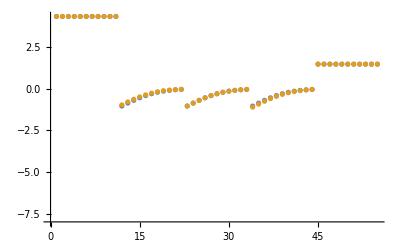

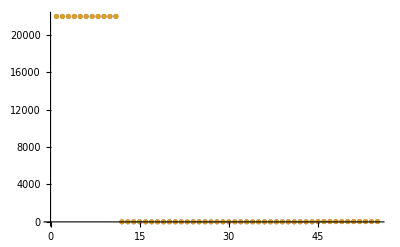

```mathematica
dataSetI=1;
ListPlot[Log10[{fittingData[[All,-1]],filteredDataList[[dataSetI,3]]}], AxesOrigin->{0,-8}]
ListPlot[{fittingData[[All,-1]],filteredDataList[[dataSetI,3]]}, AxesOrigin->{0,-8}]
```

### Parameter Distribution

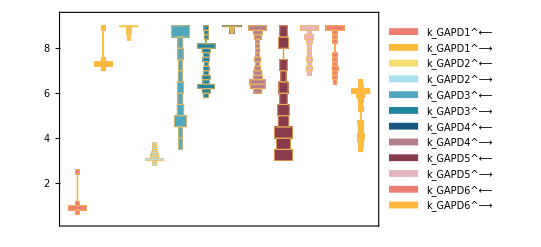

```mathematica
DistributionChart[Transpose[Log10[filteredDataList[[All,2]]]],ChartElementFunction->"HistogramDensity","PlotRange"->{-7,10},ChartLegends-> rateConstsSub[[All,2]]/.Reverse/@rateConstsSub,ChartStyle-> 24]
```

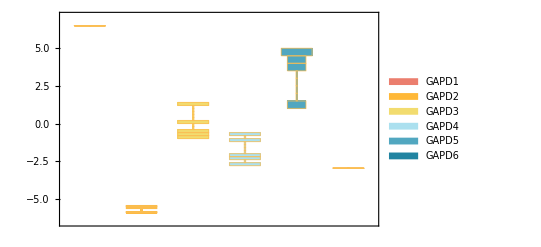

```mathematica
{ratios, plotLegend} = getElementaryKeqs[filteredDataList, rateConstsSub];
DistributionChart[Log10[Transpose@ratios],ChartElementFunction->"HistogramDensity",ChartLegends-> plotLegend,ChartStyle-> 24](*Histogram*)
```

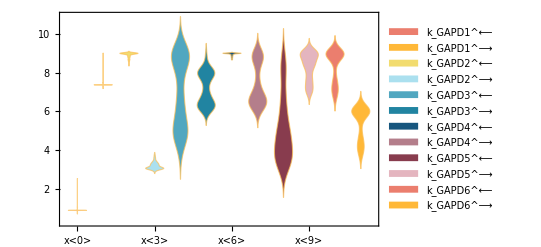

```mathematica
DistributionChart[Transpose[Log10[filteredDataList[[All,2]]]],ChartLabels-> rateConstsSub[[All,2]],"PlotRange"->{-7,10},ChartLegends-> rateConstsSub[[All,2]]/.Reverse/@rateConstsSub,ChartStyle-> 24](*Smooth*)(*If the distribution is narrow, the smooth Kernel outputs an error*)
```

### Data Error Distribution

```mathematica
errors=
Table[
	fittingData[[i,-1]]-filteredDataList[[j,3,i]],
 {j,1,Length@filteredDataList},{i,1,Length@filteredDataList[[1,3]]}];
```

```mathematica
funcNames=
Table[
	StringCases[func,RegularExpression[FileNameJoin[{inputPath , "(.*)\\.txt"}, OperatingSystem->$OperatingSystem]]->"$1"][[1]],{func,fittingData[[All,-2]]}]; (* fix later*);
```

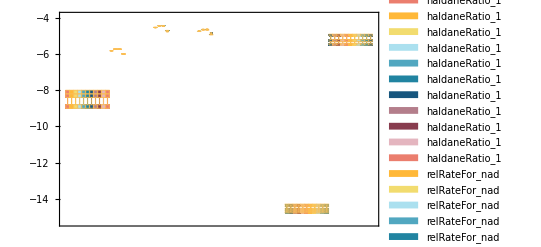

```mathematica
DistributionChart[Transpose[Log10[errors]],ChartElementFunction->"HistogramDensity",ChartLegends-> funcNames,ChartStyle-> 24](*Histogram*)
```

#### Cluster Parameters

```mathematica
(*clusters=FindClusters[Log10[filteredDataListRed[[All,2]]],Method->{"Agglomerate","Linkage"->"Complete","SignificanceTest"->{"Gap","Tolerance"->0.0001}}];(**)*)
clusters=FindClusters[Log10[filteredDataListRed[[All,2]]],Method->{"Optimize","Iterations"->2}];
medianParamCluster=Table[Median[clusters[[cluster,All,param]]],{cluster,Length[clusters]},{param,Length[clusters[[1,1]]]}](*Switch to log space and use mean?*);
clusterSqdRes=Table[(clusters[[cluster,paramSet,param]]-medianParamCluster[[cluster,param]])^2,{cluster,Length[clusters]},{paramSet,Length[clusters[[cluster]]]},{param,Length[clusters[[1,1]]]}];
clusterSSE=Table[Total[clusterSqdRes[[cluster,paramSet]]],{cluster,Length[clusterSqdRes]},{paramSet,Length[clusterSqdRes[[cluster]]]}];
bestClusterSSE=Table[SortBy[clusterSSE[[cluster]],Less],{cluster,Length[clusterSSE]}][[All,1]];
finalClusterParams={};
Table[If[clusterSSE[[cluster,paramSet]]==bestClusterSSE[[cluster]],finalClusterParams=Append[finalClusterParams,clusters[[cluster,paramSet]]]],{cluster,Length[clusterSSE]},{paramSet,Length[clusterSSE[[cluster]]]}];
```

#### Print Representative Parameter Sets for Each Cluster (Optional)

```mathematica
TableForm[finalClusterParams]
```

0.504033 | 6.84334 | 9. | 3.48477 | 3.72945 | 5.60742 | 8.98508 | 2.55274 | 8.71335 | 6.81329 | 3.3998 | 8.6853
0.302665 | 6.83612 | 9. | 2.49847 | 3.41773 | 5.57282 | 8.4452 | 8.21223 | 8.48635 | 9. | 8.72988 | 5.91734
0.403565 | 6.84537 | 8.93702 | 2.89026 | 3.79923 | 5.61764 | 8.93001 | 2.9612 | 4.37591 | 7.10803 | 2.61941 | 3.29776
0.596512 | 6.9085 | 8.99485 | 2.61851 | 5.40864 | 6.11723 | 8.99485 | 4.0603 | 2.01656 | 6.35182 | 7.98972 | 7.59992
0.530106 | 6.83522 | 8.99996 | 2.63507 | 3.36523 | 5.56857 | 9. | 3.06996 | 4.14564 | 5.88599 | 6.34476 | 8.04601

#### Parameter Cluster Plots (Optional)

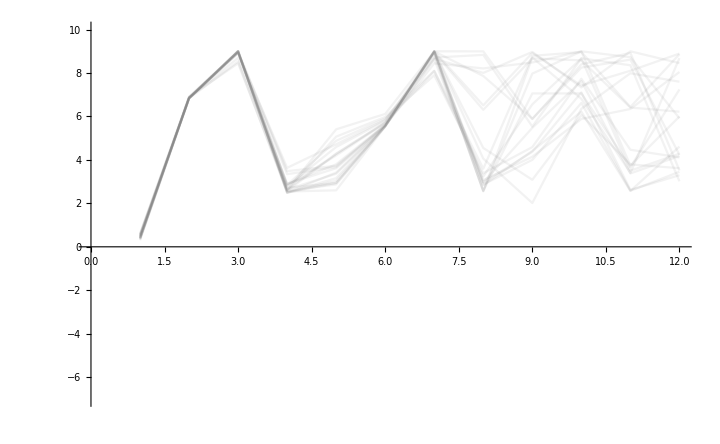

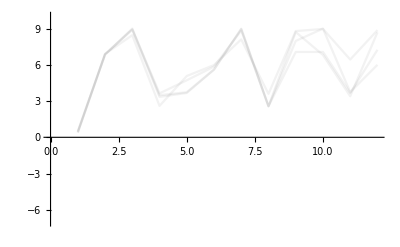
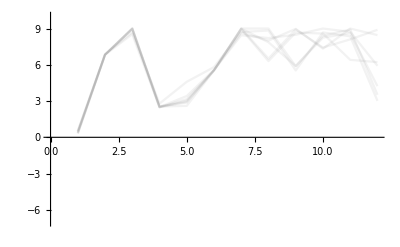
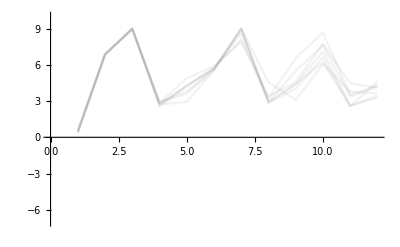
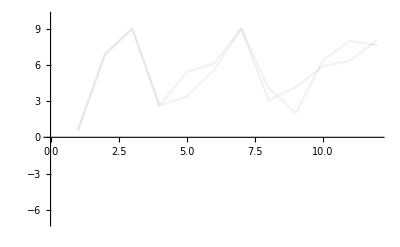

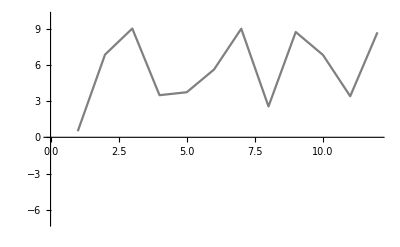
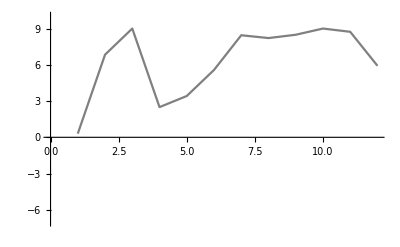
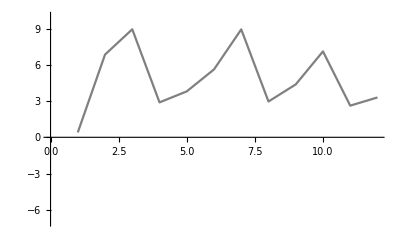

```mathematica
ListPlot[Log10[filteredDataListRed[[All,2]]],"Joined"-> True,"PlotRange"->{-7,10},PlotStyle->Opacity[.1,Gray]](*All parameter sets*)
ListPlot[#,"Joined"-> True,"PlotRange"->{-7,10},PlotStyle->Opacity[.1,Gray]]&/@clusters
(*All parameter set clusters*)
ListPlot[#,"Joined"-> True,"PlotRange"->{-7,10},PlotStyle->Opacity[1,Gray]]&/@finalClusterParams(*Representative parameter sets*)
```

### Recalculate Enzyme Parameters for all Candidate Rate Constant Sets

```mathematica
enzymeSub= parameter[rxnName<>"_total"]-> 1;
assumedSaturatingConc=1;
paramSet = 1;
dataHeader = Import[dataFilePath][[1]];
paramFitSub=Thread[rateConstsSub[[All,1]]->filteredDataList[[paramSet,2]]];
```

```mathematica
backCalculateKms[rxn, kmList, relativeRateForward, relativeRateReverse,metSatForSub, metSatRevSub, paramFitSub, assumedSaturatingConc, rxnName]//TableForm
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

General::stop: Further output of Solve::ratnz will be suppressed during this calculation.

data value | predicted value | error in %
0.000045 | 0.000044999 | 0.00221258
0.00089 | 0.00088961 | 0.0437753
0.00053 | 0.000529862 | 0.0260516

```mathematica
backCalculateKcats[rxn, kcatList, absoluteRateForward, absoluteRateReverse, paramFitSub, enzymeSub, assumedSaturatingConc]//TableForm
```

data value | predicted value | error in %
1059.36 | 1059.36 | 9.69228×10^-6

```mathematica
backCalculateRatios[haldaneRatiosList[[1]], KeqList[[1,3]], paramFitSub]//TableForm
```

data value | predicted value | error in %
0.452 | 0.452 | 2.37024×10^-7

```mathematica
backCalculateRatios[haldaneRatiosList[[1]], KeqList[[1]][[3]], paramFitSub]//TableForm
```

data value | predicted value | error in %
0.452 | 0.452 | 2.37024×10^-7

```mathematica
backCalculateKic[fittingData, filteredDataList[[1]], dataHeader, inhibitionList]//TableForm
```

data value | predicted value | error in %

```mathematica
backCalculateKiu[fittingData, filteredDataList[[1]], dataHeader, inhibitionList]//TableForm
```

data value | predicted value | error in %

#### Export rate back calculated parameter error distribution

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

General::stop: Further output of Solve::ratnz will be suppressed during this calculation.

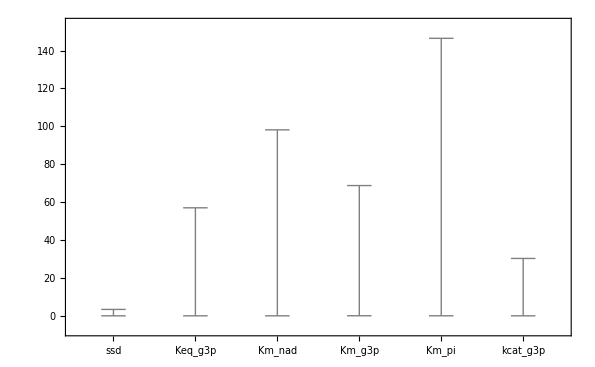

```mathematica
dataHeader = Import[dataFilePath][[1]];

{predictedParameters, predictedParameterErrors} = exportPredictedParametersAndErrors[rxn, rxnName, fitLabel, flagFitType, numFits,KeqList, kmList,s05List, kcatList, inhibitionList, otherParmsList, absoluteRateForward, absoluteRateReverse, relativeRateForward, relativeRateReverse, haldaneRatiosList,  metSatForSub, metSatRevSub, rateConstsSub, assumedSaturatingConc, fittingData, filteredDataList, dataHeader];

BoxWhiskerChart[Transpose@predictedParameterErrors[[3;;]], ChartLabels->{predictedParameterErrors[[1]]}]
```

## Export data

```mathematica
directoryExport = "C:\\Users\\Daniel Zielinski\\Desktop\\MASSpy Work\\"
CreateDirectory[directoryExport<>ToLowerCase[rxnName]]
indexLastGoodFit = 10;
```

C:\Users\Daniel Zielinski\Desktop\MASSpy Work\

C:\Users\Daniel Zielinski\Desktop\MASSpy Work\pyk2

```mathematica
rateConstsString = ToString/@rateConstsSub[[All,1]];
Export[directoryExport <>ToLowerCase[rxnName]<>"\\rateconst_labels_"<>ToLowerCase[rxnName]<>".txt",rateConstsString]
```

C:\Users\Daniel Zielinski\Desktop\MASSpy Work\pyk2\rateconst_labels_pyk2.txt

```mathematica
Export[directoryExport <>ToLowerCase[rxnName]<>"\\S_"<>ToLowerCase[rxnName]<>".txt",S[enzymeModel]]
```

C:\Users\Daniel Zielinski\Desktop\MASSpy Work\pyk2\S_pyk2.txt

```mathematica
ToString/@getSpecies[enzymeModel]
Export[directoryExport <>ToLowerCase[rxnName]<>"\\species_"<>ToLowerCase[rxnName]<>".txt",ToString/@getSpecies[enzymeModel]]
```

{E_PYK2[c],E_PYK2[c]&adp,E_PYK2[c]&atp,E_PYK2[c]&pep&adp,adp[c],atp[c],pep[c],pyr[c],E_PYK2[c]&pyr&atp}

C:\Users\Daniel Zielinski\Desktop\MASSpy Work\pyk2\species_pyk2.txt

```mathematica
ToString/@getReactions[enzymeModel]
Export[directoryExport <>ToLowerCase[rxnName]<>"\\reactions_"<>ToLowerCase[rxnName]<>".txt",ToString/@getReactions[enzymeModel]]
```

{PYK21: adp[c] + E_PYK2[c] <=> E_PYK2[c]&adp,PYK22: E_PYK2[c]&atp <=> atp[c] + E_PYK2[c],PYK23: E_PYK2[c]&adp + pep[c] <=> E_PYK2[c]&pep&adp,PYK24: E_PYK2[c]&pyr&atp <=> E_PYK2[c]&atp + pyr[c],PYK25: E_PYK2[c]&pep&adp <=> E_PYK2[c]&pyr&atp}

C:\Users\Daniel Zielinski\Desktop\MASSpy Work\pyk2\reactions_pyk2.txt

```mathematica
solEnz = Import["C:/MASSef/examples/"<>mainFolder <>"/input/enzSol_"<>rxnName<>"_.m"];
```

```mathematica
speciesStrings = ToString/@solEnz[[All,1]]
Export[directoryExport <>ToLowerCase[rxnName]<>"\\equation_labels_"<>ToLowerCase[rxnName]<>".txt",ToString/@solEnz[[All,1]]];
```

{E_PYK2[c],E_PYK2[c]&adp,E_PYK2[c]&atp,E_PYK2[c]&pep&adp,E_PYK2[c]&pyr&atp}

```mathematica
pythonSubList = Thread[Variables[solEnz[[1,2]]]->(ToString/@Variables[solEnz[[1,2]]])];
ToPython[solEnz[[1,2]]/.pythonSubList]
Do[
Export[directoryExport <>ToLowerCase[rxnName]<>"\\equation_"<>speciesStrings[[i]]<>"_"<>ToLowerCase[rxnName]<>".txt",ToPython[solEnz[[i,2]]/.pythonSubList]];,{i,1,Length[solEnz]}]
```

-((-(k_PYK21_rev*k_PYK22_fwd*k_PYK23_rev*k_PYK24_fwd*param_PYK2_total) - k_PYK21_rev*k_PYK22_fwd*k_PYK24_fwd*k_PYK25_fwd*param_PYK2_total - k_PYK21_rev*k_PYK22_fwd*k_PYK23_rev*k_PYK25_rev*param_PYK2_total - k_PYK22_fwd*k_PYK23_fwd*k_PYK24_fwd*k_PYK25_fwd*param_PYK2_total*pep(c) - k_PYK21_rev*k_PYK23_rev*k_PYK24_rev*k_PYK25_rev*param_PYK2_total*pyr(c))/(adp(c)*k_PYK21_fwd*k_PYK22_fwd*k_PYK23_rev*k_PYK24_fwd + k_PYK21_rev*k_PYK22_fwd*k_PYK23_rev*k_PYK24_fwd + atp(c)*k_PYK21_rev*k_PYK22_rev*k_PYK23_rev*k_PYK24_fwd + adp(c)*k_PYK21_fwd*k_PYK22_fwd*k_PYK24_fwd*k_PYK25_fwd + k_PYK21_rev*k_PYK22_fwd*k_PYK24_fwd*k_PYK25_fwd + atp(c)*k_PYK21_rev*k_PYK22_rev*k_PYK24_fwd*k_PYK25_fwd + adp(c)*k_PYK21_fwd*k_PYK22_fwd*k_PYK23_rev*k_PYK25_rev + k_PYK21_rev*k_PYK22_fwd*k_PYK23_rev*k_PYK25_rev + atp(c)*k_PYK21_rev*k_PYK22_rev*k_PYK23_rev*k_PYK25_rev + adp(c)*k_PYK21_fwd*k_PYK22_fwd*k_PYK23_fwd*k_PYK24_fwd*pep(c) + adp(c)*k_PYK21_fwd*k_PYK22_fwd*k_PYK23_fwd*k_PYK25_fwd*pep(c) + adp(c)*k_PYK21_fwd*k_PYK23_fwd*k_PYK24_fwd*k_PYK25_fwd*pep(c) + k_PYK22_fwd*k_PYK23_fwd*k_PYK24_fwd*k_PYK25_fwd*pep(c) + atp(c)*k_PYK22_rev*k_PYK23_fwd*k_PYK24_fwd*k_PYK25_fwd*pep(c) + adp(c)*k_PYK21_fwd*k_PYK22_fwd*k_PYK23_fwd*k_PYK25_rev*pep(c) + atp(c)*k_PYK21_rev*k_PYK22_rev*k_PYK23_rev*k_PYK24_rev*pyr(c) + atp(c)*k_PYK21_rev*k_PYK22_rev*k_PYK24_rev*k_PYK25_fwd*pyr(c) + atp(c)*k_PYK21_rev*k_PYK22_rev*k_PYK24_rev*k_PYK25_rev*pyr(c) + adp(c)*k_PYK21_fwd*k_PYK23_rev*k_PYK24_rev*k_PYK25_rev*pyr(c) + k_PYK21_rev*k_PYK23_rev*k_PYK24_rev*k_PYK25_rev*pyr(c) + atp(c)*k_PYK22_rev*k_PYK23_rev*k_PYK24_rev*k_PYK25_rev*pyr(c) + adp(c)*k_PYK21_fwd*k_PYK23_fwd*k_PYK24_rev*k_PYK25_fwd*pep(c)*pyr(c) + atp(c)*k_PYK22_rev*k_PYK23_fwd*k_PYK24_rev*k_PYK25_fwd*pep(c)*pyr(c) + adp(c)*k_PYK21_fwd*k_PYK23_fwd*k_PYK24_rev*k_PYK25_rev*pep(c)*pyr(c) + atp(c)*k_PYK22_rev*k_PYK23_fwd*k_PYK24_rev*k_PYK25_rev*pep(c)*pyr(c)))

```mathematica
(*NEED TO GRAB THE RATE CONST DATA FROM CLUSTERS*)
```

```mathematica
Export[directoryExport <>ToLowerCase[rxnName]<>"\\rateconst_clusters_"<>ToLowerCase[rxnName]<>".txt",filteredDataList[[1;;indexLastGoodFit,2]]]
```

C:\Users\Daniel Zielinski\Desktop\MASSpy Work\pyk2\rateconst_clusters_pyk2.txt

```mathematica
solRateEq = Import["C:/MASSef/examples/"<>mainFolder <>"/input/absoluteFlux_"<>rxnName<>"_.m"];
pythonSubList = Thread[Variables[solRateEq[[2]]]->(ToString/@Variables[solRateEq[[2]]])];
Export[directoryExport <>ToLowerCase[rxnName]<>"\\rateLaw_"<>ToLowerCase[rxnName]<>".txt",ToPython[solRateEq[[2]]/.pythonSubList]]
```

C:\Users\Daniel Zielinski\Desktop\MASSpy Work\pyk2\rateLaw_pyk2.txt